# Работа с экспериментальными данными

## Получение данных из изображения

```mathematica
image=Import@FileNameJoin@{NotebookDirectory[],"Безымянный.png"};
```

```mathematica
image
```

-Graphics-

```mathematica
{{1, 2, 4, 0}, {5, □, □, □}, {4, □, □, □}, {90, □, □, □}}
```

{{1,2,4,0},{5,□,□,□},{4,□,□,□},{90,□,□,□}}

```mathematica
Head@image
```

Image

```mathematica
imageData=1-ImageData@Binarize@image;
```

```mathematica
col={0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0};
Total[N@col*Range@Length@col]/Total@col
```

12.5

```mathematica
pointsForPlot=(imageDataᵀ.N@Range[Length@imageData,1,-1])/Replace[Total@imageData,0->1,{1}];
```

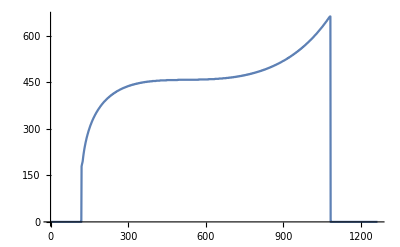

```mathematica
ListLinePlot@pointsForPlot
```

Цель — получить из изображения графика набор точек.

```mathematica
(({{0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {1, 1, 0, 1, 1}, {1, 0, 0, 1, 1}, {0, 0, 0, 0, 0}})ᵀ.Range[5,1,-1])/(Total@({{0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {1, 1, 0, 1, 1}, {1, 0, 0, 1, 1}, {0, 0, 0, 0, 0}}))
```

{5/2,7/2,4,3,5/2}

## База данных

```mathematica
raw=Import[FileNameJoin@{NotebookDirectory[],"f1.xlsx"}]⟦1⟧
```

{{T,sigma,dsigma},{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}

```mathematica
makeDataset@raw_:=With[{
header=raw⟦1⟧,
data=raw⟦2;;⟧
},
<|Thread[header->#]|>&/@data//Dataset
]
```

```mathematica
Thread[{"T","sigma","dsigma"}->{299.6,64.44130680000004,1.5474830694493167}]
```

{T→299.6,sigma→64.4413,dsigma→1.54748}

```mathematica
dataset=makeDataset@raw
```

```mathematica
dataset[Sort/*Reverse,(#T)^2&]
```

```mathematica
dataset[Select[Abs[#T-320]<2&]]
```

```mathematica
dataset@f
```

f[{<|T→299.6,sigma→64.4413,dsigma→1.54748|>,<|T→305.4,sigma→62.9813,dsigma→1.51584|>,<|T→310.3,sigma→61.9384,dsigma→1.49119|>,<|T→315.3,sigma→60.0612,dsigma→1.44681|>,<|T→320.2,sigma→58.3926,dsigma→1.4128|>,<|T→325.2,sigma→56.5154,dsigma→1.36017|>,<|T→330.,sigma→54.0124,dsigma→1.31413|>}]

```mathematica
(#T)^2&@<|"T"->299.6,"sigma"->64.44130680000004,"dsigma"->1.5474830694493167|>
```

89760.2

```mathematica
dataset[All,<|"T"->#T,"around"->Around[#sigma,#dsigma]|>&]
```

```mathematica
dataset[All,Append[#,"around"->Around[#sigma,#dsigma]]&]
```

```mathematica
dataset[All,{"T",Around[#sigma,#dsigma]&}]
```